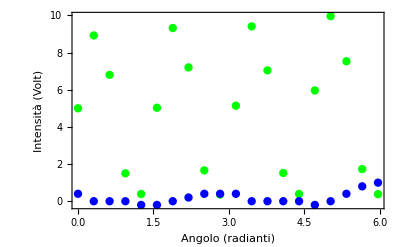

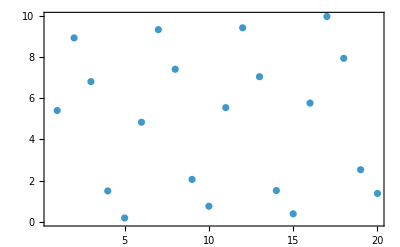

```mathematica
theta=({0, 18, 36, 54, 72 , 90, 108, 126, 144, 162, 180, 198, 216, 234, 252, 270, 288, 306, 324, 342})/180 Pi;
(*Scotando di un grado la prima misura viene un fit un po' più preciso (18 -> 17)*)
(*LAMBDA  / 
int1 =({0.30,4.64, 8.84, 7.12, 1.79, 0.32, 4.79, 9.01, 7.19, 1.70, 0.38, 5.00, 9.09, 7.00, 1.63, 0.37, 4.92, 9.16,  7.30, 1.84}- 0.03)/ 8.96;
int2=({ 9.23,4.65, 0.21, 2.18, 7.97, 9.49, 4.72, 0.22, 2.21, 8.05, 9.46, 4.49, 0.14, 2.45, 8.21, 9.58, 4.76, 0.20, 2.23, 8.09} - 0.04)/ 9.67;*)
(*LAMBDA / 4
int1 = ({2.41,4.30, 3.25, 0.74, 0.23, 2.38, 4.34, 3.39, 0.84, 0.19 , 2.37, 4.27, 3.30, 0.78, 0.22, 2.50, 4.50, 3.55, 0.88, 0.20} - 0.04) /8.96;
int2 = ({6.90,4.79, 5.97, 8.63, 9.09, 6.74, 4.77, 5.94, 8.80, 9.49, 7.08, 4.88, 6.05, 8.88, 9.56, 7.01, 4.79, 5.86, 8.71, 9.36} - 0.03) /  9.67;*)
(*RIFLESSIONE LAMBDA / 4*)*)
int1 = ({5.03,8.95, 6.83, 1.53, 0.42, 5.06, 9.35, 7.23, 1.69, 0.39, 5.17, 9.44, 7.07, 1.55, 0.42, 5.99, 9.99, 7.56, 1.76, 0.41} -  0.03);
(*RIFLESSIONE LAMBDA / 2*)
int2 = ({0.05,0.03, 0.03,0.03,0.02,0.02,0.03,0.04,0.05,0.05,0.05,0.03,0.03,0.03,0.03,0.02,0.03,0.05,0.07,0.08} - 0.03) *20;
datay=Transpose[{theta,int1}];
dataz=Transpose[{theta,int2}];
intensity=ListPlot[{datay,
 dataz},Axes->False, Frame->True,PlotRange->All,PlotStyle->{{Green,PointSize[0.015]},{Blue,PointSize[0.015]}},FrameLabel->{"Angolo (radianti)","Intensità (Volt)"}, LabelStyle -> Directive[Black, Medium], Background-> White]
valori = ListPlot[int1+int2,Axes->False, Frame->True,PlotRange->All, Background -> White, LabelStyle -> Directive[Black, Medium]]
(*SetDirectory["~/Scrivania/Gruppo19"];
Export["valori_intensità-Lambda_mezzi.svg",intensity];
Export["intensità_totale-Lambda_mezzi.svg",  valori];*)
```

Parametri:  {a→9.52688,b→2.0034,p→8.68127,o→0.00288783}

Errori (1 sigma):  {0.191894,0.00558747,0.0187928,0.117324}

Somma degli scarti quadratici:  1.46816

R^2:  0.997846

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Parametri:  {a→0.310548,b→1.77423,p→-0.886368,o→0.00281103}

Errori (1 sigma):  {0.213292,0.18677,0.629219,0.137172}

Somma degli scarti quadratici:  1.46816

R^2:  0.313406

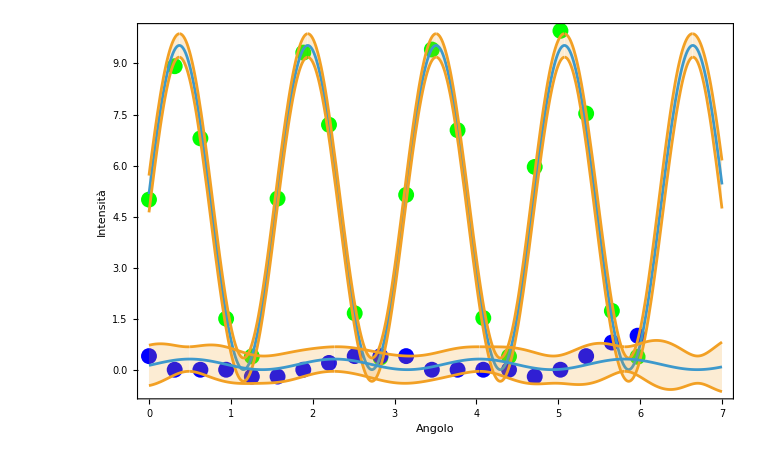

grafico dei residui

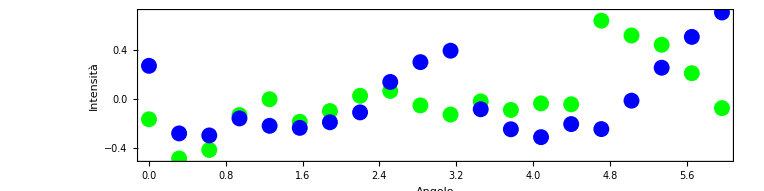

R^2:  0.999084

Parametri:  {a→0.49736,b→1.99613,p→0.841784,o→0.490292}

Errori (1 sigma):  {0.00741113,0.0041632,0.0139936,0.00454485}

Somma degli scarti quadratici:  0.00164293

R^2:  0.999809

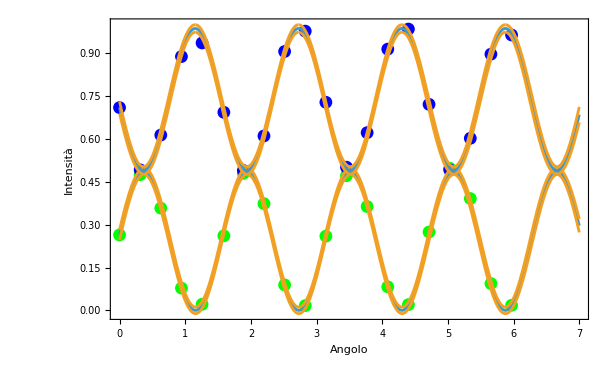

grafico dei residui

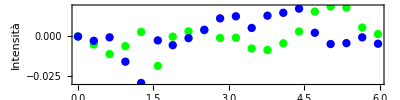

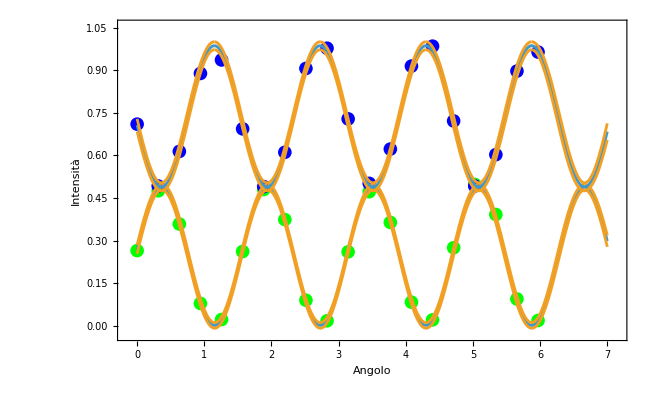

grafico dei residui

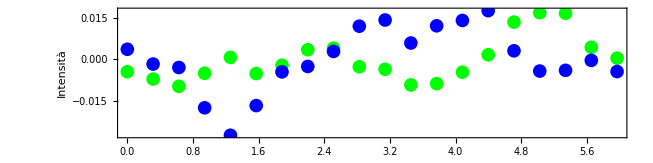

```mathematica
"La funzione di fit è   aCos[bx+p]^2+o  , dove x rappresenta l'angolo θ. I valori iniziali dei parametri di fit possono essere variati, in particolare il valore iniziale di della fase p.";

fit=NonlinearModelFit[datay,a Cos[ b x+p]^2+o,{{a, 1},{b,2},{p,1.5},{o,0}},x,ConfidenceLevel->.67];
gfit=Plot[Normal[fit],{x,Min[theta],Max[theta]},Axes->False,Frame->True,PlotRange->All,PlotStyle->{Red}];
{bands67[x_],bands99[x_],bands997[x_]}=Table[fit["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.67,.99,.997}}];
Print["Parametri:  ",fit["BestFitParameters"]]
Print["Errori (1 sigma):  ",fit["ParameterErrors"]]
err=Transpose[fit["ParameterConfidenceIntervals"]];(err[[2]]-err[[1]])/2;
res=fit["FitResiduals"];Print["Somma degli scarti quadratici:  ",Total[res^2]]
Print["R^2:  ",fit["RSquared"]]
fit1=NonlinearModelFit[dataz,a Cos[ b x+p]^2+o,{{a,1},{b,2},{p,0},{o, 0}},x,ConfidenceLevel->.67];
gfit=Plot[Normal[fit],{x,Min[theta],Max[theta]},Axes->False,Frame->True,PlotRange->All,PlotStyle->{Red}];
{bands167[x_],bands199[x_],bands1997[x_]}=Table[fit1["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.67,.99,.997}}];
Print["Parametri:  ",fit1["BestFitParameters"]]
Print["Errori (1 sigma):  ",fit1["ParameterErrors"]]
err=Transpose[fit1["ParameterConfidenceIntervals"]];(err[[2]]-err[[1]])/2;
res1=fit1["FitResiduals"];Print["Somma degli scarti quadratici:  ",Total[res^2]]
Print["R^2:  ",fit1["RSquared"]]
graphfin=Show[intensity,Plot[{fit[x],bands99[x]},{x,0,7},Filling->{2->{1}}],Plot[{fit1[x],bands199[x]},{x,0,7},Filling->{2->{1}}],FrameLabel->{"Angolo","Intensità"},LabelStyle->Directive[Black, Medium],PlotRange-> All, Background -> White]
Print["grafico dei residui"]
graphres =ListPlot[{Transpose[{theta,res}],Transpose[{theta,res1}]},Axes->False,Frame->True,PlotStyle->{{Green,PointSize[0.015]},{Blue,PointSize[0.015]}},FrameLabel->{"Angolo","Intensità"},LabelStyle->Directive[Black, Medium],AspectRatio->1/4, Background-> White]
(*SetDirectory["~/Scrivania/Gruppo19"];
Export["grafico_funzioni-Lambda_mezzi.svg",graphfin];
Export["grafico_residui-Lambda_mezzi.svg", graphres];*)
```

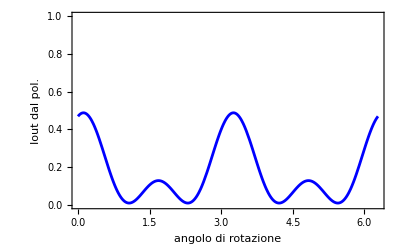

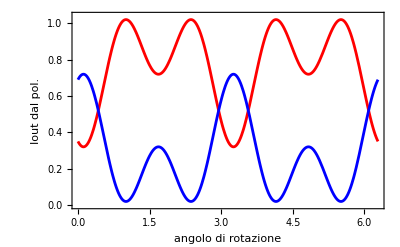

```mathematica
"Programma per il calcolo della polarizzazione in uscita da una sequenza di lamine, scritto in forma matriciale. ini è il campo in ingresso alla lamina, phi è lo sfasamento prodotto dalla lamina.";
laminam[phi_,theta_ ]:={{(Cos[theta - 0.9]^2+Exp[ⅈ phi]Sin[theta - 0.9]^2), Sin[theta - 0.9]Cos[theta - 0.9](1-Exp[ⅈ phi])},{Sin[theta - 0.9]Cos[theta- 0.9](1-Exp[ⅈ phi] ),(Sin[theta- 0.9]^2+Exp[ⅈ phi]Cos[theta-0.9]^2) }}
(*ini={1,ⅈ 0.005}; Per lambda / 4*)
(*ini = {1, ⅈ 0.2}; Per lambda / 2*)
l4=Abs[ini.laminam[Pi / 2,thet]]^2; 
l2=Abs[ini.laminam[2.1Pi  + 0.8,thet]]^2;
"Lamina lambda/2";
gL2 = Plot[{l2[[2]]},{thet,0,2Pi},Axes->False, Frame->True,PlotRange->{0,1},FrameLabel->{"angolo di rotazione","Iout dal pol."},LabelStyle->Directive[Black,Medium],PlotStyle->{Red,Blue}, Background-> White]
"Lamina lambda/4";
gL4 = Plot[{l4[[1]],l4[[2]]},{thet,0,2Pi},Axes->False, Frame->True,PlotRange->{0,Norm[ini]^2},FrameLabel->{"angolo di rotazione","Iout dal pol."},LabelStyle->Directive[Black,Medium],PlotStyle->{Red,Blue}, Background-> White]
(*
SetDirectory["~/Scrivania/Gruppo19"];
Export["lambda_mezzi.svg",gL2];
Export["lambda_quarti.svg", gL4];*)
```

```mathematica
-
```